1 - 6 Elastic deformations
Given A in a deformation y = A x, find the principal directions and corresponding factors of extension or contraction.

1.  (3.0 | 1.5
1.5 | 3.0)

```mathematica
ClearAll["Global`*"]
```

```mathematica
aA=({{3.0, 1.5}, {1.5, 3.0}})
```

{{3.,1.5},{1.5,3.}}

```mathematica
e1={vals,vecs}=Eigensystem[aA]
```

{{4.5,1.5},{{0.707107,0.707107},{-0.707107,0.707107}}}

Above: The answer agrees with the text. As explained in the s.m., the eigenvalues describe the magnitude of the deformation, and the eigenvectors describe the angle of application.

```mathematica
α=ArcCot[0.7071067811865475/0.7071067811865475]
```

```mathematica
0.7853981633974483
```

```mathematica
α/Degree
```

45.

```mathematica
β=ArcCot[-0.7071067811865475/0.7071067811865475]
```

-0.785398

```mathematica
β/Degree
```

-45.

Above: So the 4.5 magnitude distortion is directed along an axis of 45 degrees (from horizontal), and the 1.5 magnitude distortion is directed along an axis of -45 degrees.

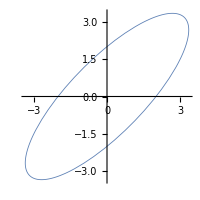

```mathematica
ParametricPlot[{4.5 Cos[t] Cos[π/4]-1.5 Sin[t] Sin[π/4],4.5 Cos[t] Sin[π/4]+1.5 Sin[t] Cos[π/4]},{t,0,2 π},ImageSize->200,PlotStyle->Thickness[0.003]]
```

3.  (7 | √6
√6 | 2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
aA=({{7, √6}, {√6, 2}})
```

{{7,√6},{√6,2}}

```mathematica
e1={vals,vecs}=Eigensystem[aA]
```

{{8,1},{{√6,1},{-1/(√6),1}}}

Above: The eigenvalues and eigenvectors match the answer in the text.

```mathematica
e1[[2,1,1]]
```

√6

```mathematica
e2=α=ArcCot[e1[[2,1,1]]/e1[[2,1,2]]]//N
```

0.387597

```mathematica
e3=e2/Degree
```

22.2077

Above: So the distortion of magnitude 8 is directed along an axis of +22.2 degrees above horizontal.

```mathematica
e1[[2,2]]
```

{-1/(√6),1}

```mathematica
e4=β=ArcCot[e1[[2,2,1]]/e1[[2,2,2]]]//N
```

-1.1832

```mathematica
e5=e4/Degree
```

-67.7923

Above: And the distortion of magnitude 1 is directed along an axis of -67.8 degrees above horizontal.

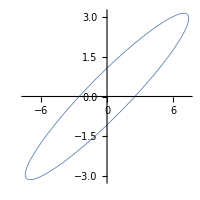

```mathematica
ParametricPlot[{8. Cos[t] Cos[.387]-1 Sin[t] Sin[.387],8. Cos[t] Sin[.387]+1 Sin[t] Cos[.387]},{t,0,2 π},ImageSize->200,PlotStyle->Thickness[0.003]]
```

5.  (1 | 1/2
1/2 | 1)

```mathematica
ClearAll["Global`*"]
```

```mathematica
aA=({{1, 1/2}, {1/2, 1}})
```

{{1,1/2},{1/2,1}}

```mathematica
e1={vals,vecs}=Eigensystem[aA]
```

{{3/2,1/2},{{1,1},{-1,1}}}

Above: The eigenvalues and eigenvectors agree with the answer in the text.

```mathematica
vecs[[1,1]]
```

1

```mathematica
e2=ArcCot[vecs[[1,1]]/vecs[[1,2]]]
```

π/4

Above: So, the distortion of magnitude 3/2 is directed along an axis rotated +45 degrees.

```mathematica
e3=ArcCot[vecs[[2,1]]/vecs[[2,2]]]
```

-π/4

And the distortion of magnitude 1/2 is directed along an axis rotated -45 degrees.

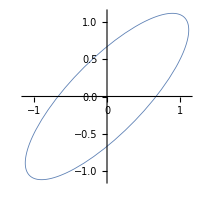

```mathematica
ParametricPlot[{3/2 Cos[t] Cos[π/4]-1/2 Sin[t] Sin[π/4],3/2 Cos[t] Sin[π/4]+1/2 Sin[t] Cos[π/4]},{t,0,2 π},ImageSize->200,PlotStyle->Thickness[0.003]]
```

7 - 9 Markov processes
Find the limit state of the Markov process modeled by the given matrix.

7.  (0.2 | 0.5
0.8 | 0.5)

Comment: The below closely follows the process and arguments of example 2 on p. 331 of the text.

```mathematica
ClearAll["Global`*"]
```

```mathematica
aA=({{0.2, 0.5}, {0.8, 0.5}})
```

{{0.2,0.5},{0.8,0.5}}

```mathematica
e1=Transpose[aA]
```

{{0.2,0.8},{0.5,0.5}}

```mathematica
e2={1,1}
```

{1,1}

```mathematica
e3=e1.e2
```

{1.,1.}

Above: Because the transpose of aA, multiplied against a unity vector, equals the unity vector, it is concluded that the transpose of aA has 1 as an eigenvalue. And because the transpose of aA has 1 as an eigenvalue, then aA also has 1 as an eigenvalue in consequence of theorem 3 in section 8.1, p. 328.

```mathematica
e4=aA-IdentityMatrix[2]
```

{{-0.8,0.5},{0.8,-0.5}}

Above: The first step in identifying the eigenvector corresponding to the eigenvalue 1 for aA, the existence of which was established.

```mathematica
e5=RowReduce[e4]
```

{{1,-0.625},{0,0}}

Above: The second step.

```mathematica
e6={x1,x2}
```

{x1,x2}

Above: Bringing the last player onto the stage.

```mathematica
e7=Thread[e4.e6==0]
```

{-0.8 x1+0.5 x2==0,0.8 x1-0.5 x2==0}

Above: e5 has an empty row. This empty row means that one coordinate of the eigenvector for eigenvalue 1 can be assigned arbitrarily.

```mathematica
e8=Solve[e7,{x1,x2}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→0.+1.6 x1}}

Above: The assignment will be for x1=5.

```mathematica
e9=e8/.x1->5
```

{{x2→8.}}

Above: The answers for the eigenvector corresponding to eigenvalue 1 for aA agrees with the text. The eigenvector is {5, 8}.

9.  (0.6 | 0.1 | 0.2
0.4 | 0.1 | 0.4
0 | 0.8 | 0.4)

```mathematica
ClearAll["Global`*"]
```

```mathematica
aA=({{0.6, 0.1, 0.2}, {0.4, 0.1, 0.4}, {0, 0.8, 0.4}})
```

{{0.6,0.1,0.2},{0.4,0.1,0.4},{0,0.8,0.4}}

```mathematica
e1=Transpose[aA]
```

{{0.6,0.4,0},{0.1,0.1,0.8},{0.2,0.4,0.4}}

```mathematica
e2=e1.{1,1,1}
```

{1.,1.,1.}

```mathematica
e3=aA-IdentityMatrix[3]
```

{{-0.4,0.1,0.2},{0.4,-0.9,0.4},{0,0.8,-0.6}}

```mathematica
e4=RowReduce[e3]
```

{{1,0.,-0.6875},{0,1,-0.75},{0,0,0}}

Above: There is an empty row in the row echelon version of aA.

```mathematica
e5={x1,x2,x3}
```

{x1,x2,x3}

```mathematica
e6=Thread[e4.e5==0]
```

{0.+x1-0.6875 x3==0,x2-0.75 x3==0,True}

```mathematica
e7=Solve[e6,e5]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→0.+1.09091 x1,x3→0.+1.45455 x1}}

```mathematica
e8=e7/.x1->11
```

Above: Since I have the answer to refer to, I know that x1 coordinate should be 11.

{{x2→12.,x3→16.}}

Above: The answer matches the text. The eigenvector sought equals {11,12,16}

10 - 12 Age-specific population
Find the growth rate in the Leslie model (see example 3, p. 331) with the matrix as given.

11.  (0 | 3.45 | 0.6
0.90 | 0 | 0
0 | 0.45 | 0)

```mathematica
ClearAll["Global`*"]
```

```mathematica
aA=({{0, 3.45, 0.6}, {0.90, 0, 0}, {0, 0.45, 0}})
```

{{0,3.45,0.6},{0.9,0,0},{0,0.45,0}}

```mathematica
e1={400,400,400}
```

{400,400,400}

```mathematica
e2=aA.e1
```

{1620.,360.,180.}

```mathematica
e3=aA.e2
```

{1350.,1458.,162.}

```mathematica
e4=aA.e3
```

{5127.3,1215.,656.1}

```mathematica
e6=Det[{{-LL, 3.45, 0.6}, {0.90, -LL, 0}, {0, 0.45, -LL}}]
```

1. (0.243+3.105 LL-1. LL^3)

```mathematica
e7=Solve[e6==0]
```

{{LL→-1.72158},{LL→-0.0784162},{LL→1.8}}

Above: There is one positive root, LL=1.8.

```mathematica
e8=aA-1.8 IdentityMatrix[3]
```

{{-1.8,3.45,0.6},{0.9,-1.8,0.},{0.,0.45,-1.8}}

```mathematica
e9={x1,x2,x3}
```

{x1,x2,x3}

```mathematica
e10=Thread[e8.e9==0]
```

{-1.8 x1+3.45 x2+0.6 x3==0,0.+0.9 x1-1.8 x2==0,0.+0.45 x2-1.8 x3==0}

```mathematica
e11=Solve[e10]
```

{{x2→0.+0.5 x1,x3→0.+0.125 x1}}

```mathematica
e12=e11/.x1->1
```

{{x2→0.5,x3→0.125}}

```mathematica
e13={1,.5,.125}
```

{1,0.5,0.125}

```mathematica
e14=1/1.625
```

0.615385

```mathematica
e15=1200 e14
```

738.462

Above: This number has to be multiplied by the first coordinate of the eigenvector: 1.

```mathematica
e16=e15 .5
```

369.231

Above: This number has to be multiplied by the second coordinate of the eigenvector: 0.5.

```mathematica
e17=e15 .125
```

92.3077

Above: This number has to be multiplied by the third coordinate of the eigenvector: .125.

```mathematica
e18=e15+e16+e17
```

1200.

Above: The three initial classes are shown to be equal to the original number.

Above: By an odd coincidence, the eigenvalue-derived factor (which is the sum of the eigenvector coordinates) WAS exactly the same for this problem as for the example 3 on p 331.  As for the problem answer, the book only gives the eigenvalue, 1.8. This value is shown as e7[[3]]. As for the calculation of initial class sizes for ‘proportional growth’, it took awhile to figure that one out.

```mathematica
2.3/.4
```

5.75

```mathematica
3.45/.6
```

5.75

```mathematica
.6/.3
```

2.

```mathematica
.9/.45
```

2.

The ‘odd coincidence’ noted above is explained. The matrices (text example/text problem) have linearly dependent entries for key locations.

13 - 15 Leontief models

13.  Leontief input-output model. suppose that three industries are interrelated so that their outputs are used as inputs by themselves, according to the 3 × 3 consumption matrix

(0.1 | 0.5 | 0
0.8 | 0 | 0.4
0.1 | 0.5 | 0.6)
where a_jk is the fraction of the output of industry k consumed (purchased) by industry j. Let p_j be the price charged by industry  j for its total output. A problem is to find prices so that for each industry, total expenditures equal total income. Show that this leads to A p = p, where p = {{p_1, p_2, p_3 }}†, and find a solution p with nonnegative p_1, p_2, p_3.

This problem would consist of finding an eigenvalue equal to 1, like the Markov problem.

```mathematica
ClearAll["Global`*"]
```

```mathematica
aA=({{0.1, 0.5, 0}, {0.8, 0, 0.4}, {0.1, 0.5, 0.6}})
```

{{0.1,0.5,0},{0.8,0,0.4},{0.1,0.5,0.6}}

```mathematica
e1=Transpose[aA]
```

{{0.1,0.8,0.1},{0.5,0,0.5},{0,0.4,0.6}}

```mathematica
e2={1,1,1}
```

{1,1,1}

```mathematica
e3=e1.e2
```

{1.,1.,1.}

Above: So the transpose has an eigenvalue equal to 1, implying that the matrix aA also has one. Now to find it.

```mathematica
e4=aA-IdentityMatrix[3]
```

{{-0.9,0.5,0},{0.8,-1,0.4},{0.1,0.5,-0.4}}

```mathematica
e5=RowReduce[e4]
```

{{1,0.,-0.4},{0,1,-0.72},{0,0,0}}

```mathematica
e6={x1,x2,x3}
```

{x1,x2,x3}

```mathematica
e7=Thread[e5.e6==0]
```

{0.+x1-0.4 x3==0,x2-0.72 x3==0,True}

```mathematica
e8=Solve[e7,e6]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→0.+1.8 x1,x3→0.+2.5 x1}}

```mathematica
e9=e8/.x1->10
```

{{x2→18.,x3→25.}}

Above: The answer matches the text. (The 10 of course was taken from the answer.)

```mathematica
738 .125
```

92.25